```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls"
};
(*equations[pars[-8]]*)
```

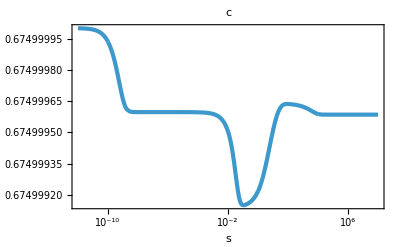
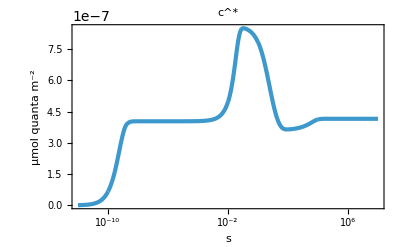
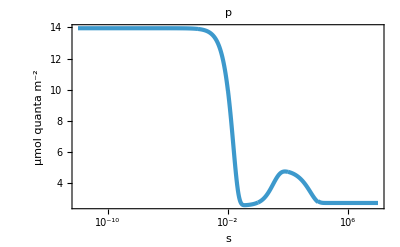
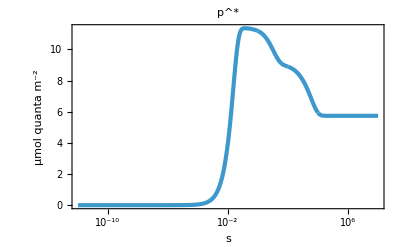
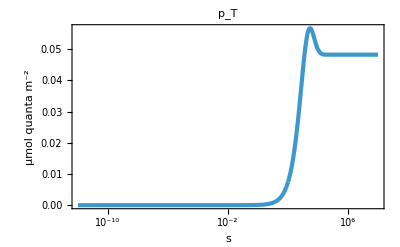
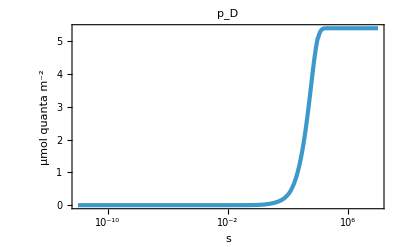
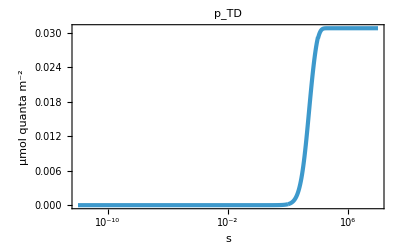
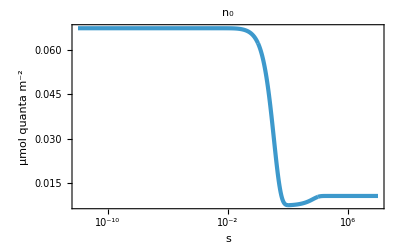

```mathematica
(Export[NotebookDirectory[]<>"Fig_7_simulation-all-time_scales/Fig_7.pdf",#];#)&@GridMap[plotSimulationStitch[#,Table[{Join[{L->800,tmin->0,tmax-> "tmax"/.timeRange[i]},pars[i]],{"tmin"/.timeRange[i],"tmax"/.timeRange[i]}},{i,-10,8,2}],{imageSizePadding[ImagePaddingExtra3],FrameLabel->{{#/.units,None},{"s",None}},PlotLabel->(#/.names)}]&,quants]
```